```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
```

plot2Doption

importData

jsonInfo

```mathematica
surgeExp=Import[FileNameJoin[{NotebookDirectory[],"surge.csv"}]];
tensionExp=Import[FileNameJoin[{NotebookDirectory[],"tension1.csv"}]];
heaveExp=Import[FileNameJoin[{NotebookDirectory[],"heave.csv"}]];
pitchExp=Import[FileNameJoin[{NotebookDirectory[],"pitch.csv"}]];
```

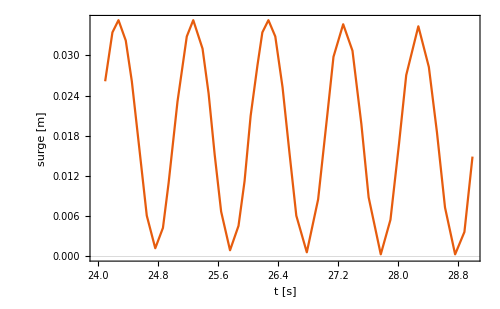

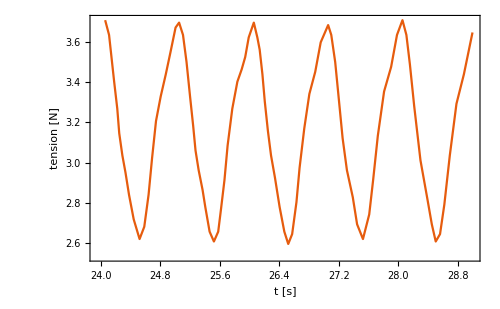

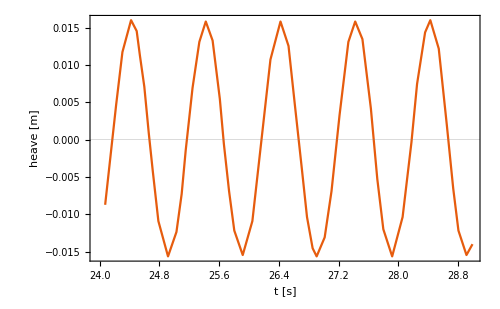

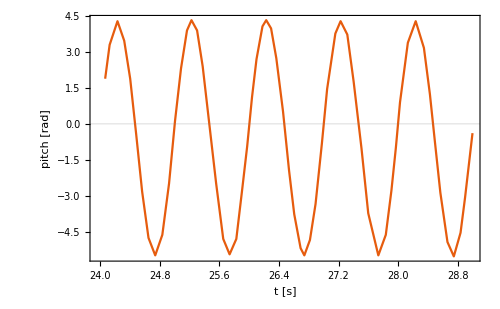

```mathematica
ListPlot[surgeExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","surge [m]"}]
ListPlot[tensionExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","tension [N]"}]
ListPlot[heaveExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","heave [m]"}]
ListPlot[pitchExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}]
```

~/BEM/Palm2016_with_mooring/result.json

no. | title | length
1 | cpu_time | 807
2 | float_COM | 807
3 | float_EK | 807
4 | float_EP | 807
5 | float_accel | 807
6 | float_area | 807
7 | float_drag_force | 807
8 | float_drag_torque | 807
9 | float_force | 807
10 | float_pitch | 807
11 | float_roll | 807
12 | float_torque | 807
13 | float_velocity | 807
14 | float_yaw | 807
15 | probe1_intersection | 807
16 | probe2_intersection | 807
17 | probe3_intersection | 807
18 | probe4_intersection | 807
19 | simulation_time | 807
20 | wall_clock_time | 807
21 | water_E | 807
22 | water_EK | 807
23 | water_EP | 807
24 | water_face_size | 807
25 | water_point_size | 807
26 | water_volume | 807

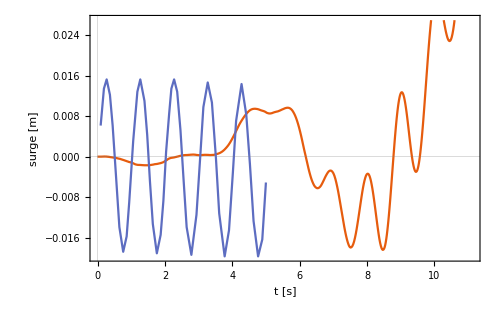

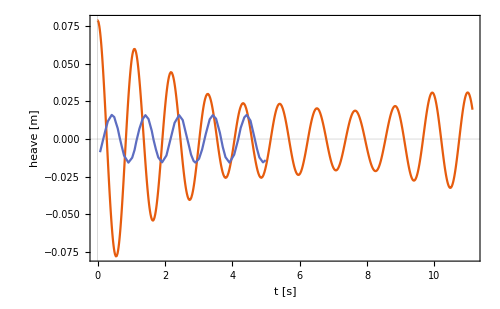

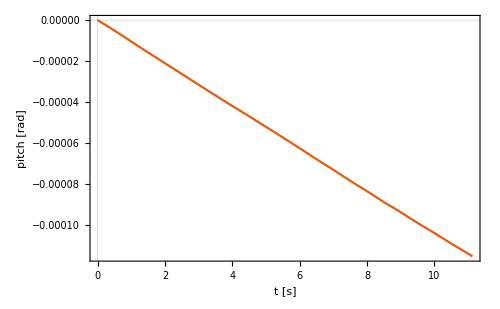

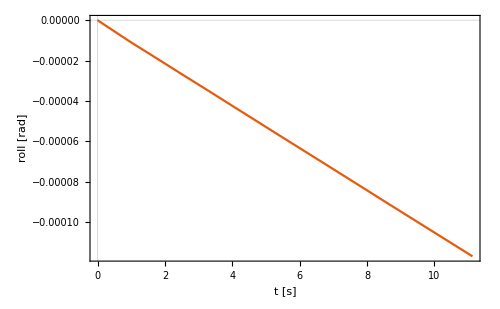

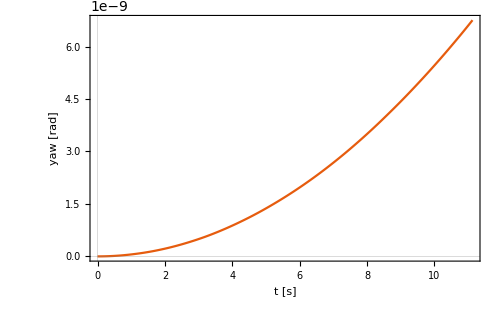

```mathematica
(*nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"*)
nameSim="~/BEM/Palm2016_with_mooring/result.json"
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

ListPlot[{Transpose@{time,surgeSim},{#1-24,#2-0.02}&@@@surgeExp},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","surge [m]"}]
ListPlot[{Transpose@{time,heaveSim-0.725},{#1-24,#2}&@@@heaveExp},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","heave [m]"}]
ListPlot[Transpose@{time,pitchSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}]
ListPlot[Transpose@{time,rollSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","roll [rad]"}]
ListPlot[Transpose@{time,yawSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","yaw [rad]"}]
```